Bretcher 1.1.10

```mathematica
Show[ContourPlot3D[{x+2y+3z==1,2x+4y+7z==2,3x+7y+11z==8},{x,-10,10},{y,-10,50},{z,-20,5},AxesLabel->{"x","y","z"},ContourStyle->Directive[Orange,Opacity[0.5],Specularity[White,30]],PlotPoints->80,Mesh->None],Graphics3D[{Red, PointSize[0.05],Point[{-9,5,0}]}]]
```

We plot the diversity with ContourPlot and highlight the intersection the solution) with a red dot.

-Graphics3D-

```mathematica
Solve[{x+2y+3z==1,2x+4y+7z==2,3x+7y+11z==8},{x,y,z}]
```

{{x→-9,y→5,z→0}}

The solution above is the point in which the 3 planes intersect.

Bretcher 1.1.11

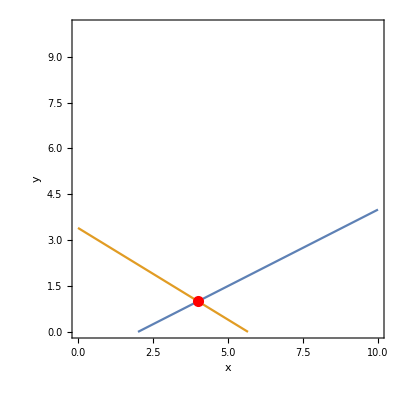

```mathematica
ContourPlot[{x-2y==2,3x+5y==17},{x,0,10},{y,0,10},AxesLabel->{"x","y"}, Epilog-> {Red, PointSize[0.02],Point[{4,1}]}]
```

```mathematica
Solve[{x-2y==2,3x+5y==17},{x,y}]
```

{{x→4,y→1}}

The intersection is x==4 and y==1.